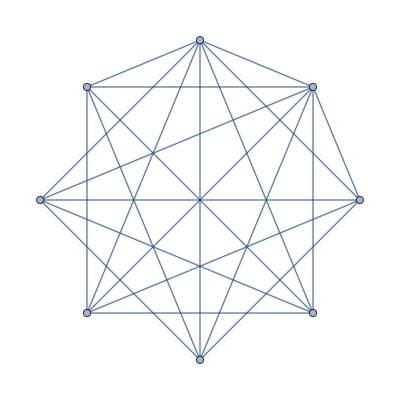

```mathematica
gr=EdgeDelete[CompleteGraph[8],EdgeList[CycleGraph[6]]]
```

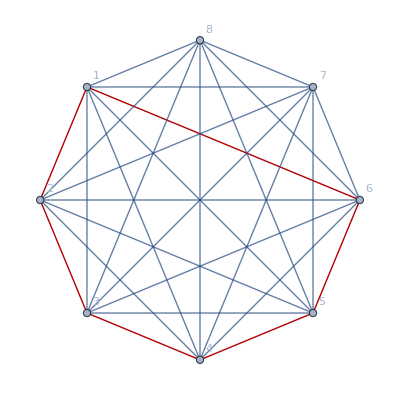
{-Graphics-,0,False}

```mathematica
With[{h=gr},{Graph[CompleteGraph[VertexCount[h]],GraphHighlight->EdgeList[GraphComplement[h]],GraphHighlightStyle->"Thick",VertexLabels->"Name"],ChromaticPolynomial[h,4],MaximalPlanarQ[h]}]
```

```mathematica
FindClique[gr]
```

{{1,3,5,7,8}}

```mathematica
MaximalPlanarQ[gr]
```

False

```mathematica
PlanarGraphQ[gr]
```

False

```mathematica
(3*VertexCount[gr]-6)
```

15

```mathematica
EdgeCount[GraphComplement[gr]]
```

5

```mathematica
3*
```

```mathematica
((VertexCount[gr]-3)*(VertexCount[gr]-4)/2)-EdgeCount[GraphComplement[gr]]
```

4

```mathematica
With[{lengthToDelete=((VertexCount[gr]-3)*(VertexCount[gr]-4)/2)-EdgeCount[GraphComplement[gr]]},Length[Subsets[EdgeList[gr],{lengthToDelete}]]]
```

7315

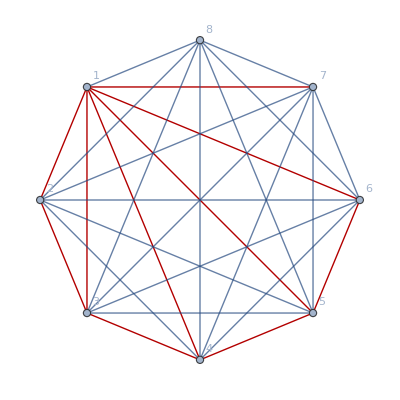
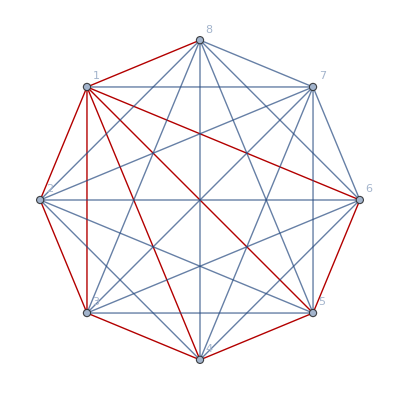
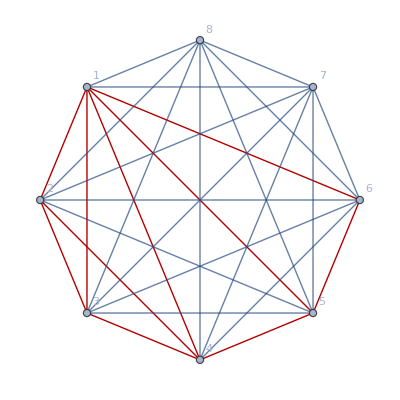
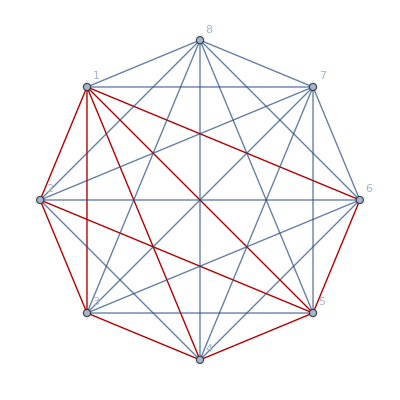
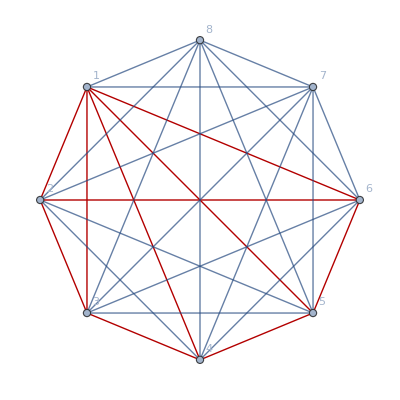
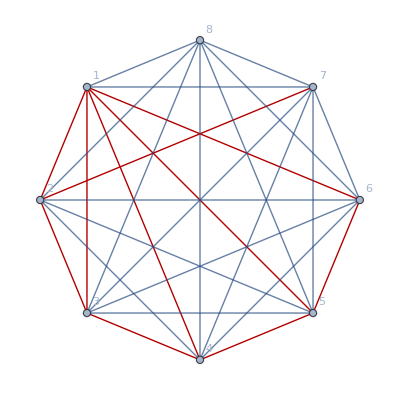
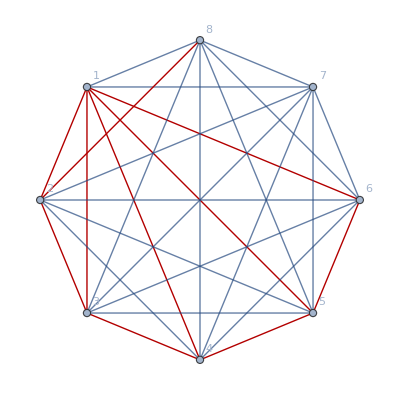
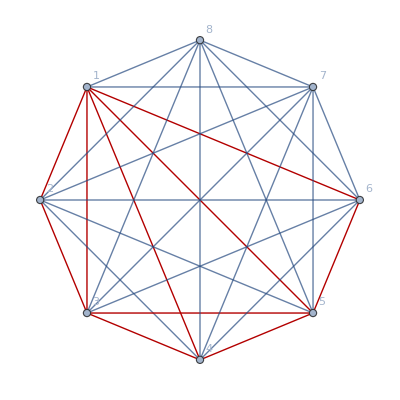
{{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,9,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,6,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,6,Non-MPG},{-Graphics-,1,Non-MPG},{-Graphics-,1,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,1,Non-MPG},{-Graphics-,1,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,3,Non-MPG},{-Graphics-,3,Non-MPG},{-Graphics-,3,Non-MPG},{-Graphics-,3,Non-MPG},{-Graphics-,13,Non-MPG},{-Graphics-,1,MPG},{-Graphics-,1,MPG},{-Graphics-,1,MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,1,MPG},{-Graphics-,1,MPG},{-Graphics-,1,MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,8,Non-MPG},{-Graphics-,1,Non-MPG},{-Graphics-,1,Non-MPG},{-Graphics-,1,MPG},{-Graphics-,1,Non-MPG},{-Graphics-,1,Non-MPG},{-Graphics-,1,Non-MPG},{-Graphics-,1,Non-MPG},{-Graphics-,1,Non-MPG},{-Graphics-,1,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,1,Non-MPG},{-Graphics-,1,Non-MPG},{-Graphics-,10,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,3,Non-MPG},{-Graphics-,3,Non-MPG},{-Graphics-,3,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,3,Non-MPG},{-Graphics-,1,Non-MPG},{-Graphics-,3,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,4,Non-MPG},{-Graphics-,7,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,3,Non-MPG},{-Graphics-,3,Non-MPG},{-Graphics-,3,Non-MPG},{-Graphics-,3,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,3,Non-MPG},{-Graphics-,1,Non-MPG},{-Graphics-,4,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,7,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,1,Non-MPG},{-Graphics-,1,MPG},{-Graphics-,1,MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,8,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,1,Non-MPG},{-Graphics-,1,Non-MPG},{-Graphics-,1,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,1,Non-MPG},{-Graphics-,1,Non-MPG},{-Graphics-,8,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,1,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,6,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,1,Non-MPG},{-Graphics-,6,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,3,Non-MPG},{-Graphics-,3,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,13,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,3,Non-MPG},{-Graphics-,3,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,3,Non-MPG},{-Graphics-,7,Non-MPG},{-Graphics-,3,Non-MPG},{-Graphics-,3,Non-MPG},{-Graphics-,3,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,7,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,5,Non-MPG},{-Graphics-,5,Non-MPG},{-Graphics-,6,Non-MPG},{-Graphics-,5,Non-MPG},{-Graphics-,5,Non-MPG},{-Graphics-,6,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,7,Non-MPG},{-Graphics-,7,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,2,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG},{-Graphics-,0,Non-MPG}}

```mathematica
With[{lengthToDelete=((VertexCount[gr]-3)*(VertexCount[gr]-4)/2)-EdgeCount[GraphComplement[gr]]},Table[With[{h=EdgeDelete[gr,e]},{Graph[CompleteGraph[VertexCount[h]],GraphHighlight->EdgeList[GraphComplement[h]],GraphHighlightStyle->"Thick",VertexLabels->"Name"],ChromaticPolynomial[h,4]/24,If[MaximalPlanarQ[h],"MPG","Non-MPG"]}],{e,Take[Subsets[EdgeList[gr],{lengthToDelete}],200]}]]
```